```mathematica
Quit[];
```

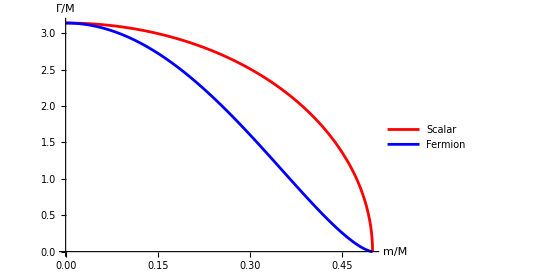

```mathematica
ScalarMaxWidth[m_]:=π(1-4 m^2)^(1/2);
FermionMaxWidth[m_]:=π(1-4 m^2)^(3/2);
Plot[{ScalarMaxWidth[m],FermionMaxWidth[m]},{m,0,1/2},PlotStyle->{Red,Blue},AspectRatio->0.7,PlotRange->Full,PlotLegends->{"Scalar","Fermion"},AxesLabel->{"m/M","Γ/M"}]
(*For safe, it is desirable that the partial width is about an order of magnitude smaller than the presented value below.*)
```

```mathematica
M0=1-0.15ⅈ;
```

```mathematica
Propagator[s_,μ_,F0_,F1_,FPrime1_]:=Abs[Im[F1[μ^2]]-Im[μ^2]FPrime1[μ^2]]/(Im[F1[μ^2]](s-μ^2)-Im[μ^2](F0[s]-F1[μ^2]));
SpectralExact[s_,μ_,F0_,F1_,FPrime1_]:=ⅈ/(2π)(Abs[Im[F1[μ^2]]-Im[μ^2]FPrime1[μ^2]]/(Im[F1[μ^2]](s-μ^2)-Im[μ^2](F0[s]-F1[μ^2]))-Abs[Im[F1[μ^2]]-Im[μ^2]FPrime1[μ^2]]/(Im[F1[μ^2]](s-μ^2)-Im[μ^2](Conjugate[F0[s]]-F1[μ^2])));
```

```mathematica
PropagatorBranch[s_,μ_,F0s_,F1s_,FPrime1s_,Rs_]:=Abs[1-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]] FPrime1s[[k]][μ^2]]/(s-μ^2-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]](F0s[[k]][s]-F1s[[k]][μ^2]));
SpectralExact[s_,μ_,F0s_,F1s_,FPrime1s_,Rs_]:=ⅈ/(2π)(Abs[1-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]] FPrime1s[[k]][μ^2]]/(s-μ^2-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]](F0s[[k]][s]-F1s[[k]][μ^2]))-Abs[1-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]] FPrime1s[[k]][μ^2]]/(s-μ^2-Im[μ^2]∑_(k=1)^Length[Rs] Rs[[k]]/Im[F1s[[k]][μ^2]](Conjugate[F0s[[k]][s]]-F1s[[k]][μ^2])));
```

```mathematica
ScalarMasslessF0[s_]:=Log[-1/s];
ScalarMasslessF1[s_]:=Log[-1/s]+2π×ⅈ;
ScalarMasslessFPrime1[s_]:=-1/s;
ScalarMasslessP[s_,μ_]:=Propagator[s,μ,ScalarMasslessF0,ScalarMasslessF1,ScalarMasslessFPrime1];
```

```mathematica
FermionMasslessF0[s_]:=s/6 Log[-1/s];
FermionMasslessF1[s_]:=s/6 (Log[-1/s]+2π×ⅈ);
FermionMasslessFPrime1[s_]:=-1/6+1/6 Log[-1/s]+1/3 π×ⅈ;
FermionMasslessP[s_,μ_]:=Propagator[s,μ,FermionMasslessF0,FermionMasslessF1,FermionMasslessFPrime1];
```

```mathematica
ScalarF0[m_,s_]:=-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))];
ScalarF1[m_,s_]:=(2 √(4 m^2-s))/(√s)(ArcTan[-(√s)/(√(4 m^2-s))]+π);
ScalarFPrime1[m_,s_]:=-1/s+(4 m^2)/(√(4 m^2-s) s^(3/2))(ArcTan[(√s)/(√(4 m^2-s))]-π);
ScalarP[m_,s_,μ_]:=Propagator[s,μ,CurryApplied[ScalarF0,2][m],CurryApplied[ScalarF1,2][m],CurryApplied[ScalarFPrime1,2][m]];
ScalarSpectralExact[m_,s_,μ_]:=SpectralExact[s,μ,CurryApplied[ScalarF0,2][m],CurryApplied[ScalarF1,2][m],CurryApplied[ScalarFPrime1,2][m]];
```

```mathematica
FermionF0[m_,s_]:=((4 m^2-s)^(3/2))/(3 √s)ArcTan[(√s)/(√(4 m^2-s))];
FermionF1[m_,s_]:=-((4 m^2-s)^(3/2))/(3 √s)(ArcTan[-(√s)/(√(4 m^2-s))]+π);
FermionFPrime1[m_,s_]:=(4 m^2-s)/(6s)-((2 m^2 +s)√(4 m^2-s))/(3 s^(3/2))(ArcTan[(√s)/(√(4 m^2-s))]-π);
FermionP[m_,s_,μ_]:=Propagator[s,μ,CurryApplied[FermionF0,2][m],CurryApplied[FermionF1,2][m],CurryApplied[FermionFPrime1,2][m]];
FermionSpectralExact[m_,s_,μ_]:=SpectralExact[s,μ,CurryApplied[FermionF0,2][m],CurryApplied[FermionF1,2][m],CurryApplied[FermionFPrime1,2][m]];
```

```mathematica
SpectralNWA[s_,μ_]:=-1/π Im[1/(s-μ^2)];
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

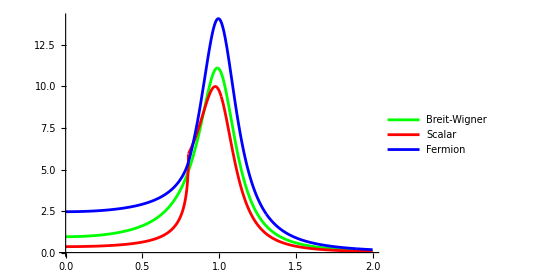

```mathematica
ParametricPlot[{{Sqrt[s],Abs[s-M0^2]^-2},{Sqrt[s],Abs[ScalarP[0.4,s,M0]]^2},{Sqrt[s],Abs[FermionP[0.4,s,M0]]^2}},{s,0,4},PlotStyle->{Green,Red,Blue},AspectRatio->0.7,PlotRange->Full,PlotLegends->{"Breit-Wigner","Scalar","Fermion"},MaxRecursion->15]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

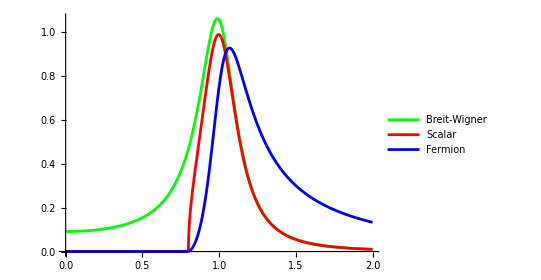

```mathematica
ParametricPlot[{{Sqrt[s],SpectralNWA[s,M0]},{Sqrt[s],ScalarSpectralExact[0.4,s,M0]},{Sqrt[s],FermionSpectralExact[0.4,s,M0]}},{s,0,4},PlotStyle->{Green,Red,Blue},AspectRatio->0.7,PlotRange->Full,PlotLegends->{"Breit-Wigner","Scalar","Fermion"},MaxRecursion->15]
```

```mathematica
FSMixP[ms_,mf_,s_,μ_,Rs_]:=PropagatorBranch[s,μ,{ScalarMasslessF0,FermionMasslessF0,CurryApplied[ScalarF0,2][ms],CurryApplied[FermionF0,2][mf]},{ScalarMasslessF1,FermionMasslessF1,CurryApplied[ScalarF1,2][ms],CurryApplied[FermionF1,2][mf]},{ScalarMasslessFPrime1,FermionMasslessFPrime1,CurryApplied[ScalarFPrime1,2][ms],CurryApplied[FermionFPrime1,2][mf]},Rs];
FSMixSpectral[ms_,mf_,s_,μ_,Rs_]:=SpectralExact[s,μ,{ScalarMasslessF0,FermionMasslessF0,CurryApplied[ScalarF0,2][ms],CurryApplied[FermionF0,2][mf]},{ScalarMasslessF1,FermionMasslessF1,CurryApplied[ScalarF1,2][ms],CurryApplied[FermionF1,2][mf]},{ScalarMasslessFPrime1,FermionMasslessFPrime1,CurryApplied[ScalarFPrime1,2][ms],CurryApplied[FermionFPrime1,2][mf]},Rs];
```

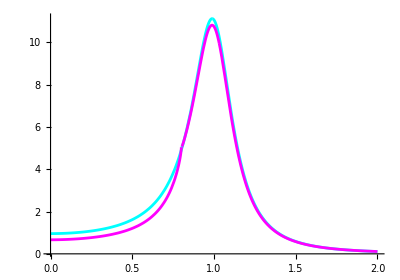

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-M0^2]^-2},{s,0,4},PlotStyle->Cyan,MaxRecursion->15],ParametricPlot[{Sqrt[s],Abs[FSMixP[0.4,0.4,s,M0,{0,0.75,0.25,0}]]^2},{s,0,4},PlotStyle->Magenta,MaxRecursion->15],AspectRatio->0.7,PlotRange->Full]
```

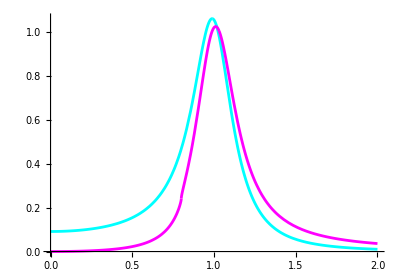

```mathematica
Show[ParametricPlot[{Sqrt[s],SpectralNWA[s,M0]},{s,0,4},PlotStyle->Cyan,MaxRecursion->15],ParametricPlot[{Sqrt[s],FSMixSpectral[0.4,0.4,s,M0,{0,0.75,0.25,0}]},{s,0,4},PlotStyle->Magenta,MaxRecursion->15],AspectRatio->0.7,PlotRange->Full]
```

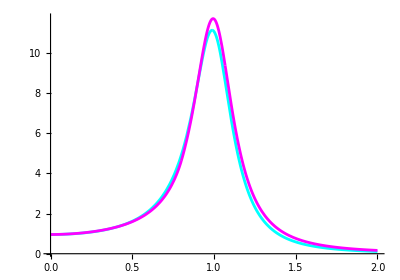

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-M0^2]^-2},{s,0,4},PlotStyle->Cyan,MaxRecursion->15],ParametricPlot[{Sqrt[s],Abs[FSMixP[0.4,0.4,s,M0,{0,0.75,0,0.25}]]^2},{s,0,4},PlotStyle->Magenta,MaxRecursion->15],AspectRatio->0.7,PlotRange->Full]
```

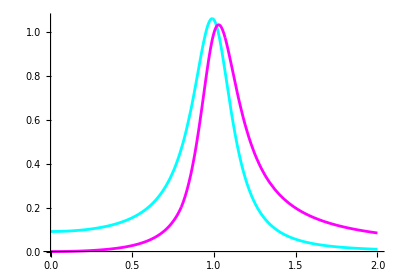

```mathematica
Show[ParametricPlot[{Sqrt[s],SpectralNWA[s,M0]},{s,0,4},PlotStyle->Cyan,MaxRecursion->15],ParametricPlot[{Sqrt[s],FSMixSpectral[0.4,0.4,s,M0,{0,0.75,0,0.25}]},{s,0,4},PlotStyle->Magenta,MaxRecursion->15],AspectRatio->0.7,PlotRange->Full]
```

```mathematica
Abs[Im[ScalarMasslessF1[M0^2]]-Im[M0^2]ScalarMasslessFPrime1[M0^2]]
```

3.16006

```mathematica
PropDen[M_,s_]:=Im[ScalarMasslessF1[M^2]](s-M^2)-Im[M^2](ScalarMasslessF0[s]-ScalarMasslessF1[M^2])
PropDen[M,s]
```

(-M^2+s) (2 π+Im[Log[-1/M^2]])-Im[M^2] (-2 ⅈ π-Log[-1/M^2]+Log[-1/s])

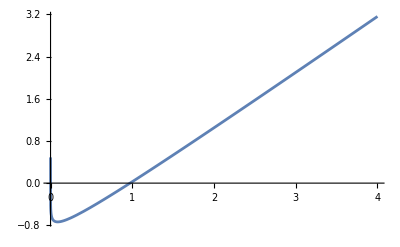

```mathematica
Plot[Re[PropDen[M0,s]]/(Abs[Im[ScalarMasslessF1[M0^2]]-Im[M0^2]ScalarMasslessFPrime1[M0^2]]),{s,0,4}]
```

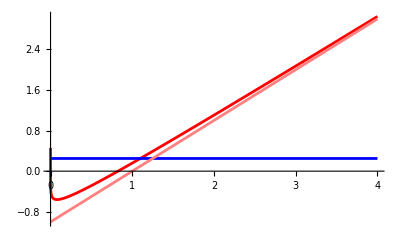

```mathematica
MSBar[M_,s_?NumericQ,alpha_]:=s-M^2+alpha/(4π)NIntegrate[Log[1/(-x(1-x)s)],{x,0,1}];
Plot[{Re[MSBar[1,s,1]],Im[MSBar[1,s,1]],s-1},{s,0,4},PlotStyle->{Red,Blue,Pink},MaxRecursion->15]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

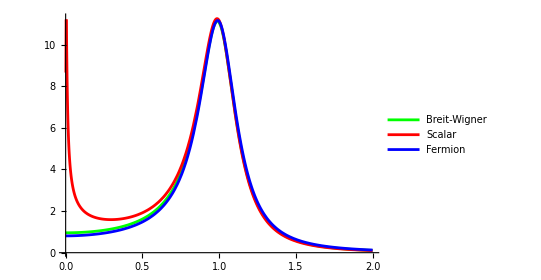

```mathematica
ParametricPlot[{{Sqrt[s],Abs[s-M0^2]^-2},{Sqrt[s],Abs[ScalarMasslessP[s,M0]]^2},{Sqrt[s],Abs[FermionMasslessP[s,M0]]^2}},{s,0,4},PlotStyle->{Green,Red,Blue},AspectRatio->0.7,PlotRange->Full,PlotLegends->{"Breit-Wigner","Scalar","Fermion"},MaxRecursion->15]
```

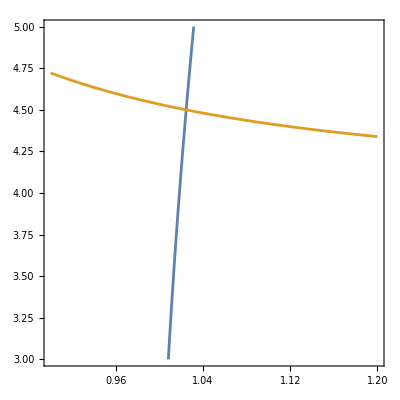

```mathematica
M0=1-0.1ⅈ;
m=0.45;
Diff[M_,g_]:=-M^2+M0^2+g^2/(16 π^2)((2 √(4 m^2-M0^2))/M0(ArcTan[-M0/(√(4 m^2-M0^2))]+π)+Re[(2 √(4 m^2-M^2))/M ArcTan[M/(√(4 m^2-M^2))]]-(M0^2-M^2)Re[-1/M^2+(4 m^2)/(√(4 m^2-M^2) M^3)ArcTan[M/(√(4 m^2-M^2))]]);
plot=ContourPlot[{Re[Diff[M,g]]==0,Im[Diff[M,g]]==0},{M,0.9,1.2},{g,3,5}]
```

```mathematica
plot//Normal//Cases[#,Line[_],Infinity]&//Apply@RegionIntersection
```

Point[{1.02446,4.50007}]

```mathematica
M0=1-0.1ⅈ;
m=0.45;
gOS=4.50007;
MOS=1.02446;
gMS=4.066;
MMS=1.172;
PiMS[g_,M_,s_]:=g^2/(16 π^2)(2+Log[1/m^2]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))]);
PiOS[g_,M_,s_]:=g^2/(16 π^2)(-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))]+Re[(2 √(4 m^2-M^2))/M ArcTan[M/(√(4 m^2-M^2))]]-(s-M^2)Re[-1/M^2+(4 m^2)/(√(4 m^2-M^2) M^3)ArcTan[M/(√(4 m^2-M^2))]]);
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

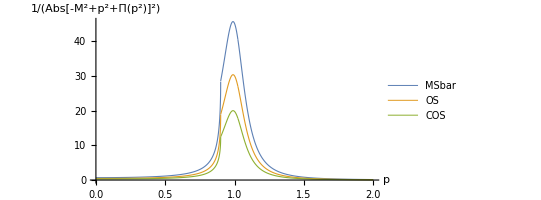

olsi1.pdf

```mathematica
olsi1=ParametricPlot[{{Sqrt[s],Abs[s-MMS^2+PiMS[gMS,MMS,s]]^-2},{Sqrt[s],Abs[s-MOS^2+PiOS[gOS,MOS,s]]^-2},{Sqrt[s],Abs[ScalarP[0.45,s,M0]]^2}},{s,0,4},PlotStyle->{Thickness[0.002],Thickness[0.002],Thickness[0.002]},AspectRatio->0.5,PlotRange->Full,PlotLegends->Placed[{"MSbar","OS","COS"},{Right,Top}],AxesLabel->{p,Abs[p^2-M^2+Π[p^2]]^-2},MaxRecursion->15]
Export["olsi1.pdf",olsi1]
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

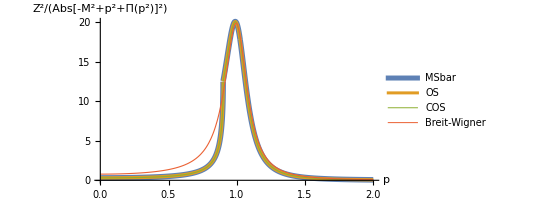

olsi2.pdf

```mathematica
olsi2=ParametricPlot[{{Sqrt[s],Abs[ScalarP[0.45,1,M0]]^2 Abs[1-MMS^2+PiMS[gMS,MMS,1]]^2 Abs[s-MMS^2+PiMS[gMS,MMS,s]]^-2},{Sqrt[s],Abs[ScalarP[0.45,1,M0]]^2 Abs[1-MOS^2+PiOS[gOS,MOS,1]]^2 Abs[s-MOS^2+PiOS[gOS,MOS,s]]^-2},{Sqrt[s],Abs[ScalarP[0.45,s,M0]]^2},{Sqrt[s],Abs[ScalarP[0.45,1,M0]]^2 Abs[1-M0^2]^2 Abs[s-M0^2]^-2}},{s,0,4},PlotStyle->{Thickness[0.010],Thickness[0.006],Thickness[0.002],Thickness[0.002]},AspectRatio->0.5,PlotRange->Full,PlotLegends->Placed[{"MSbar","OS","COS","Breit-Wigner"},{Right,Top}],AxesLabel->{p,Z^2 Abs[p^2-M^2+Π[p^2]]^-2},MaxRecursion->15]
Export["olsi2.pdf",olsi2]
```

```mathematica
PiNCOS[g_,s_]:=g^2/(16 π^2)(-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))]-(2 √(4 m^2-M0^2))/M0(ArcTan[-M0/(√(4 m^2-M0^2))]+π)-(s-M0^2)(-1/M0^2+(4 m^2)/(√(4 m^2-M0^2) M0^3)(ArcTan[M0/(√(4 m^2-M0^2))]-π)));
```

Power::infy: Infinite expression 1/(√0.) encountered.

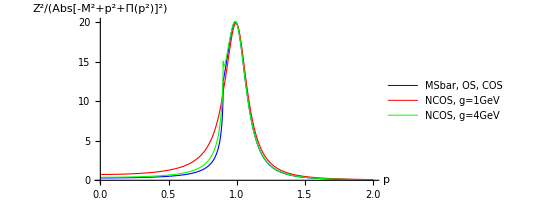

olsi3.pdf

```mathematica
olsi3=ParametricPlot[{{Sqrt[s],Abs[ScalarP[0.45,s,M0]]^2},{Sqrt[s],Abs[ScalarP[0.45,1,M0]]^2 Abs[1-M0^2+PiNCOS[1,1]]^2 Abs[s-M0^2+PiNCOS[1,s]]^-2},{Sqrt[s],Abs[ScalarP[0.45,1,M0]]^2 Abs[1-M0^2+PiNCOS[4,1]]^2 Abs[s-M0^2+PiNCOS[4,s]]^-2}},{s,0,4},PlotStyle->{Directive[Blue,Thickness[0.002]],Directive[Red,Thickness[0.002]],Directive[Green,Thickness[0.002]]},AspectRatio->0.5,PlotRange->Full,PlotLegends->Placed[{"MSbar, OS, COS","NCOS, g=1GeV","NCOS, g=4GeV"},{Right,Top}],AxesLabel->{p,Z^2 Abs[p^2-M^2+Π[p^2]]^-2},MaxRecursion->15]
Export["olsi3.pdf",olsi3]
```